{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

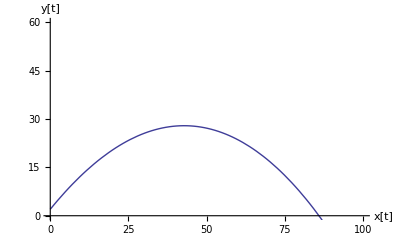

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
g=9.8; (*grav. constant*)
θ0=(50*Pi) / 180; (*50 degrees in radians*)
v0 = 30; (*starting from 30 m/s*)
vt=100;

ode1={x''[t]==(-g * x'[t]/vt^2)* Sqrt[x'[t]^2 + y'[t]^2],x[0]==0,x'[0]==v0*Cos[θ0]};
ode2 = {y''[t] == -g*(1 + (y'[t]/vt^2) * Sqrt[x'[t]^2 + y'[t]^2]), y[0] == 2, y'[0] == v0*Sin[θ0]};
sol=NDSolve[{ode1, ode2},{x,y},{t,0,200}]
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},AxesLabel->{"x[t]","y[t]"}, PlotRange -> {{0,100},{0,60}}]
```

```mathematica
ode1={x''[t]==-(g*x'[t]/vt^2)*Sqrt[x'[t]^2+y'[t]^2],x[0]==0,x'[0]==v0*Cos[θ0]};
ode2={y''[t]==-g*(1+(y'[t]/vt^2)*Sqrt[x'[t]^2+y'[t]^2]),y[0]==2,y'[0]==v0*Sin[θ0]};
xnd = x[t]==v0*Cos[θ0*t]
ynd = y[t] == 2+ v0*Sin[θ0*t] - (g*t^2)/2
Manipulate[
g = 9.8; v0 = 30; θ0 =(50*Pi)/180; vt = 35;
Module[
{sol=NDSolve[{ode1,ode2},{x,y},{t,0,200}]},ParametricPlot[Evaluate[{{x[t],y[t]}/.sol, xnd,ynd}],{t,0,tf},PlotStyle-> {{Blue},{Red}},PlotRange->{{0,100},{-10,50}},AxesLabel->{"x(m)","y (m)"},ImageSize->{500,300}]],
{{v0,30,"initial velocity (m/s)"},0,100,Appearance->"Labeled"} , {{θ0,50*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{vt,35,"terminal velocity(m/s)"},0,100.,Appearance->"Labeled"},{{tf,5.51,"time (s)"},0.01,100,Appearance->"Labeled"}]
```

x[t]==30 Cos[(5 π t)/18]

y[t]==2-4.9 t^2+30 Sin[(5 π t)/18]